```mathematica
Quit
```

```mathematica
n0=1; 
r0=1;el=1;b0=1;c=1;(*b1=0.0001;*)
```

```mathematica
n[r_]=n0*(1-(r/r0)^2)
```

1-r^2

```mathematica
Chi[x_,y_] = c/(4*Pi*n[Sqrt[x^2+y^2]]*el*y^2)
```

1/(4 π y^2 (1-x^2-y^2))

```mathematica
Chi0 =  c/(4*Pi*n0*el*r0^2);
```

```mathematica
BChi[x_,y_]=b0*r0*(Chi0/Chi[x,y])^2
```

y^4 (1-x^2-y^2)^2

```mathematica
BChiCar[x_,y_,z_,b1_]={b1, BChi[x, Sqrt[y^2+z^2]]*Sin[ArcTan[y,z]],-BChi[x, Sqrt[y^2+z^2]]*Cos[ArcTan[y,z]]}
```

{b1,z (1-x^2-y^2-z^2)^2 (y^2+z^2)^(3/2),-y (1-x^2-y^2-z^2)^2 (y^2+z^2)^(3/2)}

```mathematica
VectorPlot3D[BChiCar[x,y,z,0.01]*HeavisideTheta[r0^2-x^2-y^2-z^2],{x,-r0,r0},{y,-r0,r0},{z,-r0,r0},VectorPoints->Fine]
```

-Graphics3D-

```mathematica
CurlB[x_,y_,z_,b1_] = c/(4*Pi*n[Sqrt[x^2+y^2+z^2]]*el)*Curl[BChiCar[x,y,z,b1],{x,y,z}, "Cartesian"]
```

{(-3 y^2 (1-x^2-y^2-z^2)^2 √(y^2+z^2)-3 z^2 (1-x^2-y^2-z^2)^2 √(y^2+z^2)+4 y^2 (1-x^2-y^2-z^2) (y^2+z^2)^(3/2)+4 z^2 (1-x^2-y^2-z^2) (y^2+z^2)^(3/2)-2 (1-x^2-y^2-z^2)^2 (y^2+z^2)^(3/2))/(4 π (1-x^2-y^2-z^2)),-(x y (y^2+z^2)^(3/2))/π,-(x z (y^2+z^2)^(3/2))/π}

```mathematica
FortranForm[{1/(4 π (1-x^2-y^2-z^2))(-3 y^2 (1-x^2-y^2-z^2)^2 √(y^2+z^2)-3 z^2 (1-x^2-y^2-z^2)^2 √(y^2+z^2)+4 y^2 (1-x^2-y^2-z^2) (y^2+z^2)^(3/2)+4 z^2 (1-x^2-y^2-z^2) (y^2+z^2)^(3/2)-2 (1-x^2-y^2-z^2)^2 (y^2+z^2)^(3/2)),-(x y (y^2+z^2)^(3/2))/π,-(x z (y^2+z^2)^(3/2))/π}]
```

List((-3*y**2*(1 - x**2 - y**2 - z**2)**2*Sqrt(y**2 + z**2) - 3*z**2*(1 - x**2 - y**2 - z**2)**2*Sqrt(y**2 + z**2) + 4*y**2*(1 - x**2 - y**2 - z**2)*(y**2 + z**2)**1.5 + 
     -     4*z**2*(1 - x**2 - y**2 - z**2)*(y**2 + z**2)**1.5 - 2*(1 - x**2 - y**2 - z**2)**2*(y**2 + z**2)**1.5)/(4.*Pi*(1 - x**2 - y**2 - z**2)),-((x*y*(y**2 + z**2)**1.5)/Pi),
     -  -((x*z*(y**2 + z**2)**1.5)/Pi))

```mathematica
VectorPlot3D[CurlB[x,y,z,0.01]*HeavisideTheta[r0^2-x^2-y^2-z^2],{x,-r0,r0},{y,-r0,r0},{z,-r0,r0},VectorPoints->Fine]
```

-Graphics3D-

```mathematica
CrossT[x_,y_,z_,b1_]=Cross[CurlB[x,y,z,b1],BChiCar[x,y,z,b1]] //Simplify
```

{(x (y^2+z^2)^4 (-1+x^2+y^2+z^2)^2)/π,1/(4 π)(y^2+z^2) (9 y^11-4 b1 x z √(y^2+z^2)+y z^4 (-1+x^2+z^2)^2 (-5+5 x^2+9 z^2)+y^9 (-23+23 x^2+45 z^2)+y^7 (19+19 x^4-92 z^2+90 z^4+x^2 (-38+92 z^2))+y^3 z^2 (-10+10 x^6+57 z^2-92 z^4+45 z^6+x^4 (-30+57 z^2)+2 x^2 (15-57 z^2+46 z^4))+y^5 (-5+5 x^6+57 z^2-138 z^4+90 z^6+3 x^4 (-5+19 z^2)+3 x^2 (5-38 z^2+46 z^4))),1/(4 π)(y^2+z^2) (9 y^10 z+4 b1 x y √(y^2+z^2)+z^5 (-1+x^2+z^2)^2 (-5+5 x^2+9 z^2)+y^8 z (-23+23 x^2+45 z^2)+y^6 z (19+19 x^4-92 z^2+90 z^4+x^2 (-38+92 z^2))+y^2 z^3 (-10+10 x^6+57 z^2-92 z^4+45 z^6+x^4 (-30+57 z^2)+2 x^2 (15-57 z^2+46 z^4))+y^4 z (-5+5 x^6+57 z^2-138 z^4+90 z^6+3 x^4 (-5+19 z^2)+3 x^2 (5-38 z^2+46 z^4)))}

```mathematica
VectorPlot3D[CrossT[x,y,z,0.01]*HeavisideTheta[r0^2-x^2-y^2-z^2],{x,-r0,r0},{y,-r0,r0},{z,-r0,r0},VectorPoints->Fine]
```

-Graphics3D-

```mathematica
dBdt[x_,y_,z_,b1_]=Curl[CrossT[x,y,z,b1],{x,y,z},"Cartesian"] // FullSimplify
```

{(5 b1 x (y^2+z^2)^(3/2))/π,(-2 b1 y^3 √(y^2+z^2)-2 b1 y z^2 √(y^2+z^2)+x z (y^2+z^2)^3 (-1+x^2+y^2+z^2)^2)/(2 π),-(2 b1 y^2 z √(y^2+z^2)+2 b1 z^3 √(y^2+z^2)+x y (y^2+z^2)^3 (-1+x^2+y^2+z^2)^2)/(2 π)}

```mathematica
VectorPlot3D[Simplify[dBdt[x,y,z],b1==0.00001]*HeavisideTheta[r0^2-x^2-y^2-z^2],{x,-r0,r0},{y,-r0,r0},{z,-r0,r0},VectorPoints->Fine]
```

$Aborted

```mathematica
TransformedField["Cartesian"->"Cylindrical",{(5 b1 x (y^2+z^2)^(3/2))/π,1/(2 π)(-2 b1 y^3 √(y^2+z^2)-2 b1 y z^2 √(y^2+z^2)),-1/(2 π)(2 b1 y^2 z √(y^2+z^2)+2 b1 z^3 √(y^2+z^2))},{y,z,x}->{r,θ,ζ}]//Simplify
```

{-(b1 (r^2)^(3/2) Cos[θ] (-5 ζ+r Sin[θ]))/π,-(b1 (r^2)^(3/2) (r+r Cos[2 θ]+10 ζ Sin[θ]))/(2 π),-(b1 r^3 √(r^2) Sin[θ])/π}

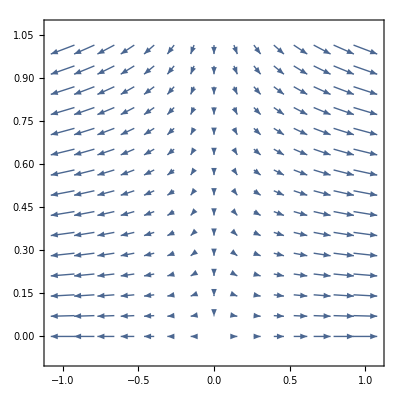

```mathematica
VectorPlot[{5x/Pi,-y/Pi},{x,-1,1},{y,0,1}]
```

```mathematica
dBdtT[dt_,b1_]= Curl[Cross[c/(4*Pi*n[Sqrt[x^2+y^2+z^2]]*el)*Curl[BChiCar[x,y,z,b1]+dBdt[x,y,z,b1]*dt,{x,y,z}, "Cartesian"],BChiCar[x,y,z,b1]+dBdt[x,y,z,b1]*dt],{x,y,z},"Cartesian"] // Simplify
```

{(b1 (40 π^2 x (y^2+z^2)^(3/2)+dt^2 x (33+187 x^2-91 y^2-91 z^2) (y^2+z^2)^(9/2)-2 dt π (y^2+z^2)^3 (-36-140 x^2+85 y^2+85 z^2)))/(8 π^3),-1/(8 π^3 (-1+x^2+y^2+z^2)^2)√(y^2+z^2) (-z (y^2+z^2)^2 (-1+x^2+y^2+z^2)^4 (4 π^2 x √(y^2+z^2)-2 dt π (y^2+z^2)^2 (-1-4 x^2+2 y^2+2 z^2)-dt^2 x (y^2+z^2)^(7/2) (-1-3 x^2+2 y^2+2 z^2))+30 b1^2 dt z (π (-1-x^2+y^2+z^2)+2 dt x (y^2+z^2)^(3/2) (-2-3 x^2+3 y^2+3 z^2))+b1 y (y^2+z^2) (-1+x^2+y^2+z^2)^2 (8 π^2+70 dt π x (y^2+z^2)^(3/2)-dt^2 (y^2+z^2)^3 (-3-51 x^2+7 y^2+7 z^2))),-1/(8 π^3 (-1+x^2+y^2+z^2)^2)√(y^2+z^2) (y (y^2+z^2)^2 (-1+x^2+y^2+z^2)^4 (4 π^2 x √(y^2+z^2)-2 dt π (y^2+z^2)^2 (-1-4 x^2+2 y^2+2 z^2)-dt^2 x (y^2+z^2)^(7/2) (-1-3 x^2+2 y^2+2 z^2))-30 b1^2 dt y (π (-1-x^2+y^2+z^2)+2 dt x (y^2+z^2)^(3/2) (-2-3 x^2+3 y^2+3 z^2))+b1 z (y^2+z^2) (-1+x^2+y^2+z^2)^2 (8 π^2+70 dt π x (y^2+z^2)^(3/2)-dt^2 (y^2+z^2)^3 (-3-51 x^2+7 y^2+7 z^2)))}

```mathematica
NewB[x_,y_,z_,T_,b1_]=BChiCar[x,y,z,b1]+Integrate[dBdtT[dt,b1],{dt,0,T}] // Simplify
```

{b1+(b1 (40 π^2 T x (y^2+z^2)^(3/2)+1/3 T^3 x (33+187 x^2-91 y^2-91 z^2) (y^2+z^2)^(9/2)-π T^2 (y^2+z^2)^3 (-36-140 x^2+85 y^2+85 z^2)))/(8 π^3),1/8 √(y^2+z^2) (8 z (y^2+z^2) (-1+x^2+y^2+z^2)^2+(z (y^2+z^2)^2 (-1+x^2+y^2+z^2)^2 (4 π^2 T x √(y^2+z^2)-π T^2 (y^2+z^2)^2 (-1-4 x^2+2 y^2+2 z^2)-1/3 T^3 x (y^2+z^2)^(7/2) (-1-3 x^2+2 y^2+2 z^2)))/π^3-(5 b1^2 T^2 z (3 π (-1-x^2+y^2+z^2)+4 T x (y^2+z^2)^(3/2) (-2-3 x^2+3 y^2+3 z^2)))/(π^3 (-1+x^2+y^2+z^2)^2)-(b1 y (y^2+z^2) (8 π^2 T+35 π T^2 x (y^2+z^2)^(3/2)-1/3 T^3 (y^2+z^2)^3 (-3-51 x^2+7 y^2+7 z^2)))/π^3),1/8 √(y^2+z^2) (-8 y (y^2+z^2) (-1+x^2+y^2+z^2)^2-(y (y^2+z^2)^2 (-1+x^2+y^2+z^2)^2 (4 π^2 T x √(y^2+z^2)-π T^2 (y^2+z^2)^2 (-1-4 x^2+2 y^2+2 z^2)-1/3 T^3 x (y^2+z^2)^(7/2) (-1-3 x^2+2 y^2+2 z^2)))/π^3+(5 b1^2 T^2 y (3 π (-1-x^2+y^2+z^2)+4 T x (y^2+z^2)^(3/2) (-2-3 x^2+3 y^2+3 z^2)))/(π^3 (-1+x^2+y^2+z^2)^2)-(b1 z (y^2+z^2) (8 π^2 T+35 π T^2 x (y^2+z^2)^(3/2)-1/3 T^3 (y^2+z^2)^3 (-3-51 x^2+7 y^2+7 z^2)))/π^3)}

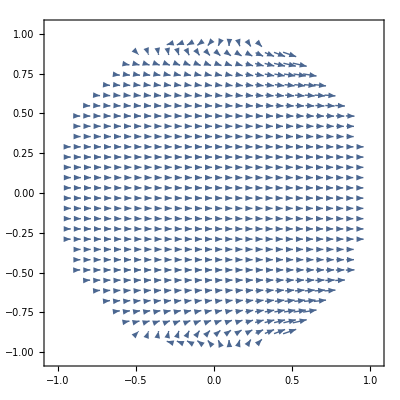

```mathematica
TT=2.;VectorPlot[{NewB[x,y,0,TT,0.01].{1,0,0}, NewB[x,y,0,TT,0.01].{0,1,0}}*HeavisideTheta[r0^2-x^2-y^2],{x,-r0,r0},{y,-r0,r0},VectorPoints->32]
```

```mathematica
FullSimplify[NewB[x,y,0,T,b1],{y>0}]
```

{(b1 (24 π^3+120 π^2 T x y^3+T^3 x y^9 (33+187 x^2-91 y^2)+3 π T^2 y^6 (36+140 x^2-85 y^2)))/(24 π^3),-(b1 T y^4 (24 π^2+105 π T x y^3+T^2 y^6 (3+51 x^2-7 y^2)))/(24 π^3),1/8 y (-8 y^3 (-1+x^2+y^2)^2-(T y^6 (-1+x^2+y^2)^2 (12 π^2 x+T^2 x y^6 (1+3 x^2-2 y^2)+3 π T y^3 (1+4 x^2-2 y^2)))/(3 π^3)-(5 b1^2 T^2 y (4 T x y^3 (2+3 x^2-3 y^2)+3 π (1+x^2-y^2)))/(π^3 (-1+x^2+y^2)^2))}

```mathematica
Series[{(24 π^3+120 π^2 T x y^3+T^3 x y^9 (33+187 x^2-91 y^2)+3 π T^2 y^6 (36+140 x^2-85 y^2))/(24 π^3),-(T y^4 (24 π^2+105 π T x y^3+T^2 y^6 (3+51 x^2-7 y^2)))/(24 π^3)},{T,0,3}]
```

{1+(5 x y^3 T)/π+((36 y^6+140 x^2 y^6-85 y^8) T^2)/(8 π^2)+((33 x y^9+187 x^3 y^9-91 x y^11) T^3)/(24 π^3)+O[T]^4,-(y^4 T)/π-(35 (x y^7) T^2)/(8 π^2)+((-3 y^10-51 x^2 y^10+7 y^12) T^3)/(24 π^3)+O[T]^4}

```mathematica
FortranForm[{1+(5 x y^3 T)/π+((36 y^6+140 x^2 y^6-85 y^8) T^2)/(8 π^2)+((33 x y^9+187 x^3 y^9-91 x y^11) T^3)/(24 π^3), -(y^4 T)/π-(35 (x y^7) T^2)/(8 π^2)+((-3 y^10-51 x^2 y^10+7 y^12) T^3)/(24 π^3)}]
```

List(1 + (5*T*x*y**3)/Pi + (T**2*(36*y**6 + 140*x**2*y**6 - 85*y**8))/(8.*Pi**2) + (T**3*(33*x*y**9 + 187*x**3*y**9 - 91*x*y**11))/(24.*Pi**3),
     -  -((T*y**4)/Pi) - (35*T**2*x*y**7)/(8.*Pi**2) + (T**3*(-3*y**10 - 51*x**2*y**10 + 7*y**12))/(24.*Pi**3))